# Further Introduction to Mathematica

Jason Harris
Wolfram Research

## Introduction

This talk will revisit some of the topics of the first day and look at several topics in pattern matching in more detail. Topics include Structure Manipulation, Scoping Constructs, Caching of Values and Performance considerations, Pure Functions with Multiple Arguments, Attributes, Sequence Objects & Matching, introduce Manipulate, discuss compilation and Parallel programming, and introducte the Notation package.

## Recap: Command Completion, Convert To, and Last Input / Output

Command completion is your friend! ⌘-K to complete the command, and ⌘-⇧-K to template-ize the command.

Complete WeierstrassP, NIntegrate, WorkingPrecision

```mathematica
1+1
```

I also use ⌘-L, to get the last input and ⌘-⇧-L to get the last output.

Also ⌘-⇧-N will convert / Canonicalize to StandardForm, whereas  ⌘-⇧-T will convert / Canonicalize to TraditionalForm.

```mathematica
1+1
```

```mathematica
Plot[f,{x,Subscript[x, min],Subscript[x, max]}]
```

```mathematica
Gamma[z]⟦1⟧
```

```mathematica
Gamma[z]
```

```mathematica
∫_a^b Sin[x]ⅆx
```

# Core Language

## Recap: Expressions

```mathematica
nb=InputNotebook[]
```

gu3fk_shm11FrontEndObject[LinkObject["gu3fk_shm", 3, 1]]11Porto 2014 JFH Lecture2.nb/Users/jason/Desktop/Porto/Talk/Porto 2014 JFH Lecture2.nb

### General Expressions

Everything inside Mathematica is an expression of the form (apart from terminals):

```mathematica
head[Subscript[argument, 1],Subscript[argument, 2],...]
```

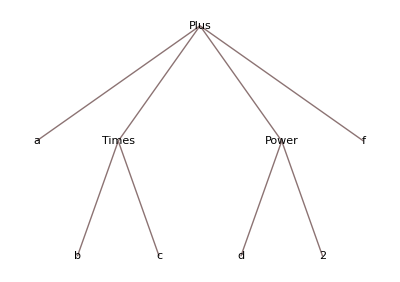

```mathematica
a+d^2+f+b*c//TreeForm
```

```mathematica
D[f[x], x]
```

f'[x]

```mathematica
FullForm @ %
```

Derivative[1][f][x]

```mathematica
Normal @ Series[Sin[x],{x,0,3}]
```

x-x^3/6

```mathematica
FullForm  @ %9
```

SeriesData[x,0,List[1,0,Rational[-1,6]],1,4,1]

```mathematica
%/.x^3->a
```

-a/6+x

Look at the full form of these last two. Try replacement in the series object for x^3

## Recap: Pure Functions

A pure function (or lambda function in other terminology) can be thought of as a small unnamed utility function.

```mathematica
MySquare[x_]:=x^2
```

```mathematica
MySquare /@ {2,f,Sin[x]}
```

{4,f^2,Sin[x]^2}

```mathematica
(a↦a^2) /@ {2,f,Sin[x]}
```

{4,f^2,Sin[x]^2}

```mathematica
(#^2&)/@ {2,f,Sin[x]}
```

{4,f^2,Sin[x]^2}

Use (a↦a^2)
Use (#^2&)

### Pure functions of more than one variable

```mathematica
({a,b}↦g[a,b^2+1])[t,w]
```

g[t,1+w^2]

```mathematica
({a,b}↦g[a,b^2+1])
```

Function[{a,b},g[a,b^2+1]]

```mathematica
Function[{a,b},g[a,b^2+1]][t,w]
```

g[t,1+w^2]

```mathematica
(g[#1,#2^2+1]&)[t,w]
```

g[t,1+w^2]

```mathematica
FullForm @ Function[{a,b},g[a,b^2+1]]
```

Function[List[a,b],g[a,Plus[Power[b,2],1]]]

```mathematica
FullForm [g[#1,#2^2+1]&]
```

Function[g[Slot[1],Plus[Power[Slot[2],2],1]]]

## Derivatives and Replacements

This came up a lot in the exercises

```mathematica
D[f[x], x]+2 D[f[x], x,x]
```

```mathematica
f'[x]+2 f''[x]/.f->(x↦x^2)
```

4+2 x

```mathematica
%/.f[x]->x^2
```

f'[x]+2 f''[x]

```mathematica
f'[x]//FullForm
```

Derivative[1][f][x]

Why isn’t this working?

Do FullForm, show replacement isn’t working, use a pure function instead

### Functionize

Write a function which turns an expression into a pure function Functionize[x^2+3x+c,x] which yields (#^2+3#+c&)

```mathematica
Functionize[expr_,x_]:=
Function@@{expr/.x->#}
```

```mathematica
x^2+3x+c/.x->#
```

```mathematica
Functionize[x^2+3x+c,x]
```

```mathematica
Function[x,c+3 x+x^2][t]
```

c+3 t+t^2

```mathematica
(c+3 #1+#1^2&)[t]
```

c+3 t+t^2

```mathematica
c+3 #1+#1^2//FullForm
```

Plus[c,Times[3,Slot[1]],Power[Slot[1],2]]

Or we could just use named variables as well so  Functionize[x^2+3x+c,x] could yield (x↦x^2+3x+c) instead.

```mathematica
ClearAll[Functionize]
Functionize[expr_,x_]:=Function[x,expr]
```

Functionize[expr_, var_] := Function @@ {expr /. var -> #}
Functionize[expr_, var_] := Function[var, expr]

## Recap: Structure Manipulation

### Map

You can use Map to map a function onto a list or more generally onto an expression. (Short form: /@)

```mathematica
a[b[g]]
```

```mathematica
g[foo]/@{a,b,c,d}
```

g[{foo[a],foo[b],foo[c],foo[d]}]

Do a map of foo over g[a,b,c,d]. Talk about g@foo and precedence of operations.

### Apply

Apply will replace the head of an expression. (Short form: @@)

```mathematica
bar@@f[g+k]
```

bar[g+k]

Apply on the children is done via @@@

```mathematica
bar@@@{foo[a],goo[b],boo[c],woo[d]}
```

{bar[a],bar[b],bar[c],bar[d]}

```mathematica
Apply[bar,{foo[a[g]],goo[b[h]],boo[c[y]],woo[d[y]]},{2}]
```

{foo[bar[g]],goo[bar[h]],boo[bar[y]],woo[bar[y]]}

### Flatten

Flatten will flatten out nested lists

```mathematica
Flatten[{a,{b,{c}},d},1]
```

{a,b,{c},d}

Flatten will takes a level parameter

Include a level parameter in the flatten

## Attributes

Attributes can be “added” to functions and they change the behavior of functions in specific ways.

### Listable Attributes

Many functions are Listable in Mathematica.

```mathematica
Plus[{1,2,3,4},{a,b,c,d}]
```

{1+a,2+b,3+c,4+d}

```mathematica
??Plus
```

x+y+z represents a sum of terms.

Attributes[Plus]={Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}
 
Default[Plus]:=0

```mathematica
Plus
```

```mathematica
SetAttributes[foo,Listable]
```

Do Power[{1,2,3,4},2] and Plus, etc. Make foo listable.

### Holding Attributes

```mathematica
ClearAll[f,g]
f[g[a_]]:=B[a]
g[x_]:=x^2
```

```mathematica
f[g[r]]
```

B[r]

```mathematica
SetAttributes[f,HoldAll]
```

By setting the HoldAll attribute on a function, it will not by default evaluate its arguments.

SetAttributes[f, HoldAll]

Other common attributes, are HoldFirst, HoldRest, HoldAllComplete

### Matching Attributes

For us, later we will revisit the attributes Flat, Orderless, and OneIdentity.

```mathematica
SetAttributes[plus,{Flat,Orderless}]
```

```mathematica
plus[b,plus[a,c]]
```

plus[a,b,c]

```mathematica
plus[a_,b_]:=g[a,b]
```

```mathematica
plus[x,y,z]
```

g[plus[x],g[plus[y],plus[z]]]

```mathematica
SetAttributes[plus,{Flat,Orderless,OneIdentity}]
```

```mathematica
plus[x,y,z]
```

g[x,g[y,z]]

```mathematica
??Plus
```

RowBox[{StyleBox["x", "TI"], "+", StyleBox["y", "TI"], "+", StyleBox["z", "TI"]}] represents a sum of terms.

Attributes[Plus]={Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}
 
Default[Plus]:=0

### Permission Attributes

```mathematica
Foo/:D[Foo[x_],x_]:=Foo[2x]^2
```

```mathematica
??Foo
```

Global`Foo

∂_x_ Foo[x_]^:=Foo[2 x]^2

```mathematica
D[Foo[t],t]
```

Foo[2 t]^2

```mathematica
ClearAttributes[D,ReadProtected]
```

ClearAttributes[D, Protected]
D[Foo[x_],x_]:=Foo[2x]^2
Foo/:D[Foo[x_],x_]:=Foo[2x]^2

## Riffle Solution

It is instructive to walk through the exercise for MyRiffle in the exercises. Riffle has the following behavior:

```mathematica
Riffle[{a,b,c,d},x]
```

{a,x,b,x,c,x,d}

```mathematica
MyRiffle[{a,b,{c,g},d},x]
```

{a,x,b,x,{c,g},x,d}

```mathematica
MyRiffle[expr_List,r_]:=Drop[Flatten[Transpose[{expr,Table[r,{Length@expr}]}],1],-1]
```

MyRiffle[a_List, x_] := Drop[Flatten[{a, Table[x, {Length @a}]}ᵀ, 1], -1]

### Pure Function Approach

```mathematica
(Drop[#,-1]&)@{t,u,u}
```

{t,u}

```mathematica
MyRiffle[a_List,x_]:=
(Drop[#,-1]&)@
(Flatten[#,1]&)@
({a,Table[x,{Length @a}]}ᵀ)
```

```mathematica
MyRiffle[a_List,x_]:=
Drop[#,-1]&@
Flatten[#,1]&@
({a,Table[x,{Length @a}]}ᵀ)
```

```mathematica
FullForm[Drop[#,-1]&@
Flatten[#,1]&]
```

Function[Function[Drop[Slot[1],-1]][Flatten[Slot[1],1]]]

```mathematica
FullForm[Hold[(Drop[#,-1]&)@(Flatten[#,1]&)]]
```

Hold[Function[Drop[Slot[1],-1]][Function[Flatten[Slot[1],1]]]]

```mathematica
MyRiffle[{a,{b,c},g,d},x]
```

{a,x,{b,c},x,g,x,d}

## Scoping

You can Localize variables with Block, Module, and With.

### The Problem

Nikolai at one time used the following:

```mathematica
f[d_]:=
Block[{x},
x/.NSolve[HermiteH[d,x] ==0,x]
]
```

```mathematica
f[4]
```

{-1.65068,-0.524648,0.524648,1.65068}

```mathematica
f[5]
```

{-2.02018,-0.958572,0.,0.958572,2.02018}

```mathematica
x=2
```

2

```mathematica
f[4]
```

2

With motivation get down to z[degree_]:=Block[{x}, x /. NSolve[HermiteH[4,x] ==0,x]]

### Block

Task return the reverse list of roots of a polynomial in some variable wrapped in fud.

```mathematica
foo[poly_,x_]->fud reverse of roots
```

```mathematica
x=2
```

2

```mathematica
foo[x^2+3 x +4==0,x]
```

Solve::ivar: 2 is not a valid variable.

ReplaceAll::reps: {Solve[False, 2]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

fud[Solve[False,2],2]

```mathematica
SetAttributes[foo,HoldAll]
foo[poly_, x_] :=
Block[{sol,x},
sol = Solve[poly, x];
fud @@ Reverse[x /. sol]
]
```

### Blocks and Modules

What is the output of:

```mathematica
yy=1;
Block[{yy},
Print @ yy;
yy=2;
Print @ yy;
]
Print @ yy;
```

yy

2

1

```mathematica
x=.
```

```mathematica
Block[{x},x^2]
```

x^2

```mathematica
Module[{x},x^2]
```

x$1277^2

Block is “dynamic” scoping and Module is “lexical” scoping. Tend to use Block.

## Fibonacci, Performance, and Timings

I am going to talk about how to gauge performance, algorithm selection, and timings.

### Simple Fibonacci

Here is a naive implementation of Fibonacci

```mathematica
ClearAll@MyFib
MyFib[n_Integer/;n>0]:=MyFib[n-1]^2+MyFib[n-2]^2
MyFib[1]=1;
MyFib[0]=0;
```

```mathematica
MyFib[8]
```

21

```mathematica
Fibonacci[8]
```

21

### Performance of Simple Fibonacci

```mathematica
timings=N/@First/@Table[Timing@MyFib[n],{n,1,30}]
```

{6.×10^-6,9.×10^-6,5.×10^-6,0.00001,0.000015,0.000026,0.000042,0.000069,0.000111,0.000179,0.000291,0.000472,0.000765,0.001318,0.002002,0.00323,0.005217,0.008662,0.013539,0.02247,0.037839,0.058118,0.093429,0.151038,0.243518,0.402411,0.640034,1.06565,1.68279,2.72378}

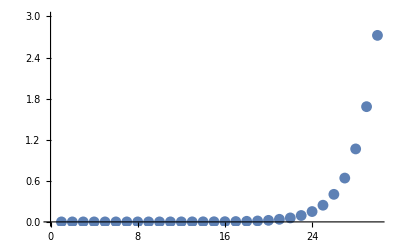

```mathematica
p1=ListPlot[timings,PlotRange->{0,3}]
```

```mathematica
theFit=a+b ⅇ^(c x)/.FindFit[timings,a+b ⅇ^(c x),{a,b,c},x]
```

-0.000458241+1.6131×10^-6 ⅇ^(0.47799 x)

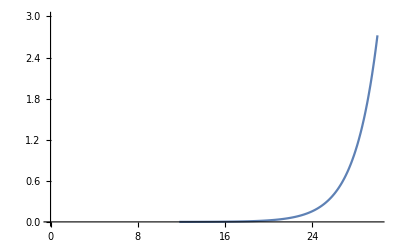

```mathematica
p2=Plot[theFit,{x,0,30},PlotRange->{0,3}]
```

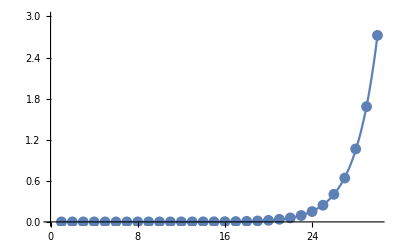

```mathematica
Show[p1,p2]
```

pts=Table[Timing @ MyFib[n],{n,1,30}]
timings =N/@First/@pts
theCoeffs= FindFit[timings,a ⅇ^(b x) +c,{a,b,c},x]
theFit = a ⅇ^(b x) +c /.theCoeffs
p1=ListPlot[timings,PlotRange→{0,3}]
p2=Plot[theFit,{x,1,30},PlotRange→{0,3}]
Show[p1,p2]

So that is quite bad performance...

### Caching Fibonacci

```mathematica
ClearAll@MyFib
MyFib[1]=1;
MyFib[0]=0;
MyFib[n_Integer/;n>0]:=
 (MyFib[n]=MyFib[n-1]+MyFib[n-2])
```

```mathematica
MyFib[700]
```

87470814955752846203978413017571327342367240967697381074230432592527501911290377655628227150878427331693193369109193672330777527943718169105124275

```mathematica
Fibonacci[700]==%
```

True

```mathematica
??MyFib
```

Cache the simple Fibonacci sequences as we compute them:
MyFib[n_Integer /; n >= 0] := MyFib[n] = MyFib[n - 1] + MyFib[n - 2]

### A More Intelligent Version

```mathematica
fib[0]:=0
fib[n_Integer/;n>0]:=fibAux[1,0,n-1];
fibAux[total_,prev_,totalSquare_,prevTotalSquare_,0]:=total;
fibAux[total_,prev_,n_]:=fibAux[total+prev,total,n-1];
```

```mathematica
My
```

```mathematica
Fibonacci[700]==fib[700]
```

True

```mathematica
IntegerLength @ fib[700]
```

146

```mathematica
??fib
```

Global`fib

fib[0]:=0
 
fib[n_Integer/;n>0]:=fibAux[1,0,n-1]

The moral here is that Mathematica will do to a large degree whatever you tell it to, and so you need to choose algorithms which are sensible.

fib[0] := 0
fib[n_Integer /; n > 0] := fibAux[1, 0, n - 1];
fibAux[total_, prev_, 0] := total;
fibAux[total_, prev_, n_] := fibAux[total + prev, total, n - 1];

### Iteration Limits

Of note using the old method this would of course take much much longer than the lifetime of the universe to compute...

```mathematica
theFit/.x->500
```

1.00453×10^98

What can we push our new algorithm to?

```mathematica
Block[{$IterationLimit=∞},
IntegerLength @ fib[1000000]]
```

208988

IntegerLength @ Block[{$IterationLimit=∞},fib[1000000]]

### Closed Form Solution

Interestingly, after doing the exercise you can determine that the closed form solution for Fibonacci[n] is:

```mathematica
(2^-n (-(1-√5)^n+(1+√5)^n))/(√5)
```

## Implementing Differentation

Let us now put much of the previous pattern matching together to implement a simple form of differentiation.

```mathematica
MyD[f_+g_,x_]:=MyD[f,x]+MyD[g,x]
MyD[f_ g_,x_]:=f MyD[g,x]+MyD[f,x]g
```

The above rules function for n-arguments through the attributes of plus and times.

```mathematica
MyD[(f+g)[x],x]
```

```mathematica
MyD[x_,x_]:=1
MyD[f_^n_Integer,x_]:=n f^(n-1)MyD[f,x]
MyD[g_[f_],x_]:=MyD[g[f],f]MyD[f,x]/;f=!=x
```

```mathematica
MyD[Cos[x_],x_]:=-Sin[x]
MyD[Sin[x_],x_]:=Cos[x]
```

```mathematica
MyD[Exp[f_],x_]:=Exp[f]MyD[f,x]
MyD[Log[f_],x_]:=MyD[f,x]/f
```

```mathematica
MyD[f_,x_]/;FreeQ[f,x]:=0
```

```mathematica
MyD[y Cos[x]+x^3 Sin[x^2]^4+x^3+ⅇ^(-Sin[x]),x]
```

3 x^2-ⅇ^(-Sin[x]) Cos[x]-y Sin[x]+8 x^4 Cos[x^2] Sin[x^2]^3+3 x^2 Sin[x^2]^4

```mathematica
D[y Cos[x]+x^3 Sin[x^2]^4+x^3+ⅇ^(-Sin[x]),x]
```

3 x^2-ⅇ^(-Sin[x]) Cos[x]-y Sin[x]+8 x^4 Cos[x^2] Sin[x^2]^3+3 x^2 Sin[x^2]^4

```mathematica
%==%%
```

True

```mathematica
FullSimplify @ %
```

x (Cos[x]-Cos[x^2]) Sin[x^2]==0

## Summary:

Choose your algorithims wisely

For matching, check the FullForm of expressions

Attributes effect the Evaluation and Pattern matching of expressions

You can exectue things in parallel

You can compile Code to the WVM, or to a C target

You can link to external C libraries